-Graphics3D-

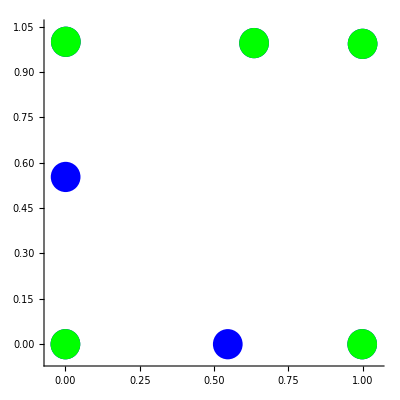

```mathematica
sr=0.05;
points=
{
{-0.194397,-0.191359,-1},{-0.194397,-0.990669,-1},{-0.194397,0.99378,-1},{-1,-0.984375,-0.512316},{-0.996208,-0.502779,-0.514612},{-0.984375,1,-0.521775},{-0.687937,0.997666,-0.701228}
};
texcoords1=
{
{0.546364,0},{0.998567,0},{-0,0},{1,0.993144},{0.634822,0.995651},{0.00141459,1},{0.000782396,0.553099}
};
texcoords2=
{
{0.998567,0},{-0,0},{1,0.993144},{0.634822,0.995651},{0.00141459,1}
};
Graphics3D[
{
Blue,
Map[Sphere[#1,sr]&,points],
Blue,
Arrow[{{-0.194397,-0.191359,-1},{-0.194397,-0.990669,-1}}],
Arrow[{{-0.194397,-0.191359,-1},{-1,-0.984375,-0.512316}}],
Red,
Arrow[{{-0.194397,-0.191359,-1},{-0.194397,-1.19136,-1}}],
Arrow[{{-0.194397,-0.191359,-1},{-1.04986,-0.191359,-0.482134}}],
Green,
Arrow[{{-0.194397,1,-1},{-0.194397,-0.990669,-1}}],
Arrow[{{-0.194397,1,-1},{-1,1,-0.512316}}]
}
]

Graphics[
{
Blue,
Map[Disk[#1,sr]&,texcoords1],
Green,
Map[Disk[#1,sr]&,texcoords2]
},
Axes->True
]
```